```mathematica
outall2g=ToExpression[Import[NotebookDirectory[]<>"out-Er-dw-coupled-Ntraj.dat","TSV"]];
outall2g//Dimensions
```

{21,11,30,500,9}

```mathematica
dims=Dimensions[outall2g]
Gs=Range[0,2,0.2];Length[Gs]
ddw=Range[-1,1,0.1];Length[ddw]
```

{21,11,30,500,9}

11

21

```mathematica
norm=dims[[1]]*dims[[3]]*dims[[4]];
```

```mathematica
(* out: toRight, toLeft , total to right *)
iRates={{4,5,7,10},{3,6,8,9}};
dims=Dimensions[outall2g];
rvsdw={};
Do[
ff [z_]:=({Gs[[i]],z});
x=Sum[outall2g[[i1,i,i3,i4,5]],{i1,1,dims[[1]]},{i3,1,dims[[3]]},{i4,1,dims[[4]]}]/norm;
Xr=Sum[x[[ii]],{ii,{4,5,7,10}}];(* to right*)
Xl=Sum[x[[ii]],{ii,{3,6,8,9}}];(* to left*)
X={ff/@{Xr},ff/@{Xl},ff/@{Xr-Xl}};
AppendTo[rvsdw,X];
,{i,1,Length[Gs]}];
```

```mathematica
rvsdw//Dimensions
```

{11,3,1,2}

```mathematica
XR=rvsdw[[;;,1,1,;;]];
XL=rvsdw[[;;,2,1,;;]];
XtR=rvsdw[[;;,3,1,;;]];
```

```mathematica
outall2ge=ToExpression[Import[NotebookDirectory[]<>"out-Er-dw-uncoupled-Ntraj.dat","TSV"]];
dimse=Dimensions[outall2ge]
Gse=Range[0,2,0.1];Length[Gse]
ddwe=Range[0,1,1];Length[ddwe]
```

{2,21,1,300,9}

21

2

```mathematica
norme=dimse[[1]]*dimse[[3]]*dimse[[4]];
```

```mathematica
(* out: toRight, toLeft , total to right *)
iRates={{4,5,7,10},{3,6,8,9}};
dimse=Dimensions[outall2ge];
rvsdwe={};
Do[
ff [z_]:=({Gse[[i]],z});
x=Sum[outall2ge[[i1,i,i3,i4,5]],{i1,1,dimse[[1]]},{i3,1,dimse[[3]]},{i4,1,dimse[[4]]}]/norme;
Xr=Sum[x[[ii]],{ii,{4,5,7,10}}];(* to right*)
Xl=Sum[x[[ii]],{ii,{3,6,8,9}}];(* to left*)
X={ff/@{Xr},ff/@{Xl},ff/@{Xr-Xl}};
AppendTo[rvsdwe,X];
,{i,1,Length[Gse]}];
```

```mathematica
rvsdwe//Dimensions
```

{21,3,1,2}

```mathematica
XRe=rvsdwe[[;;,1,1,;;]];
XLe=rvsdwe[[;;,2,1,;;]];
XtRe=rvsdwe[[;;,3,1,;;]];
```

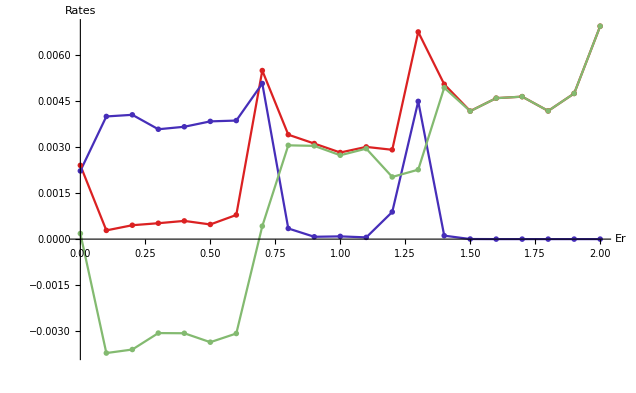

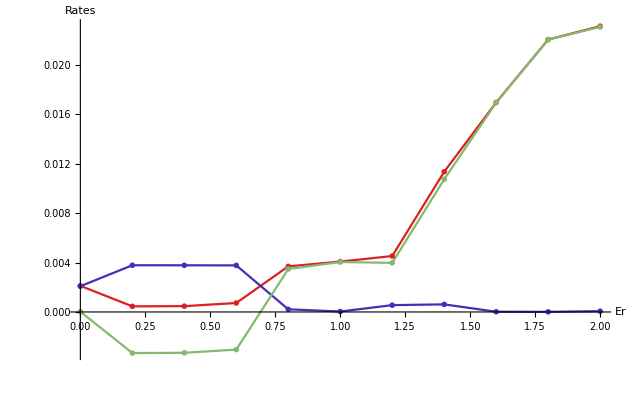

-Graphics-

```mathematica
cols={RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.513417, 0.72992, 0.440682],RGBColor[0.857359, 0.131106, 0.132128],RGBColor[0.2748608, 0.1822636, 0.7272788],RGBColor[0.513417, 0.72992, 0.440682]};ListPlot[{XRe,XLe,XtRe},Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"Er","Rates"} ]
ListPlot[{XR,XL,XtR},Joined->True,PlotStyle->cols,PlotMarkers-> cols,AxesLabel-> {"Er","Rates"} ]
ListPlot[{XRe,XLe,XtRe,XR,XL,XtR},Joined->True,PlotStyle->cols,PlotMarkers->{"Δ","Δ","Δ","Π","Π","Π"},AxesLabel-> {"Er","Rates"} ]
```